## Section | Atom-field interactions

The starting point to understand atom-field interactions is to study the coupling of a single mode field and two level atom. In the semiclassical model the atom is quantized and the field is treated as a classical field. Using dipole approximation when field wavelength is larger than atomic size, the mathematics are analogous to a spin 1/2 particle. In the same manner as a spin 1/2 particle have Rabi oscillations when interacting with a time dependent magnetic field, the two level atom shows optical Rabi oscillations. This can be shown just using a semiclassical model, but when both atom and field are quantized other phenomena arise such as “collapse and revivals”. We explore evolutions of different initial states and discuss mathematical formalisms to analyze the atom-field system.

### Key Concepts

Semiclassical models

Rabi oscillations

Jaynes-Cummings model

Dressed state basis

### Atom-field interaction processes

We consider an atom with levels   with energies  being the level  the lowest energy level interacting with  a electric field

### Absorption

Absorption happens when  an atom in a particular state goes to a higher energy level and in the process the amplitude of the electric field reduces. This is relevant when the field frequency is quasi-resonant, that is  
ω ≃ ω_ba = (E_b-E_a)/ℏ, for ω close to that frequency the model can be simplified to just a two level atom.

### Stimulated emission

Stimulated emission is the process that is the counterpart of absorption, and is also relevant when the field frequency is quasi-resonant. In this case an atom decays to a lower energy level and the field is amplified. For the field to be amplified means that a photon was emitted with the same frequency, polarization and phase as the incident field ; so they can interfere coherently.

### Spontaneous emission

Even when there is not a an electromagnetic field an atom can decay from state |b⟩ to  |a⟩, and a photon is emitted at the resonant frequency. The emitted photon leaves the atom with completely arbitrary phase and polarization. This phenomenon is introduced here for the sake of completeness, but cannot be explained until we consider interactions of an atom with a quantized field (all the modes including the vacuum).

Note: in the diagrams we are depicting photons because make the diagrams clearer, but the field that we will consider first is classical

### Semiclassical Hamiltonian models

The simplest semiclassical model  is to consider the dynamics of a single electron in the field of a stationary nucleus. The motion of the electron is described by quantum operators, while the field is taken to be classical defined by the potentials A(r,t) and U(r,t)

It can be shown using the Lagrangian formalism, that the interaction Hamiltonian that includes the field of the nucleus and also external fields takes the following form:

This Hamiltonian leads to the classical equation of motion when averages  values are calculated. There exists an infinite number of pairs {A(r,t), U(r,t)} associated with values of electric and magnetic fields, going from a pair of potentials to another valid pair is done by the so called Gauge transformations

where F(r, t)  is just a scalar field

#### Coulomb gauge and A · p Hamiltonian

It is known that there are infinite solutions that reproduce an electromagnetic field related by Gauge transformations.

Additional conditions on the potentials determines a choice of Gauge that removes the arbitrariness . One choice that is commonly used in quantum optics, is the Coulomb Gauge determined by the condition:

This choice for the vector potential is called  the transverse vector potential A_⊥(r,t ), for example in the case of plane electromagnetic wave
the Coulomb Gauge potentials    and    reproduce the E and B fields for this case. And the electric field is related to the vector potentials as:

Consider the situation of an electron evolving in an external applied field and the Coulomb potential of the nucleus. If we take the external field to be a plane wave, the nuclear electrostatic field has zero vector potential and the scalar potential is   . Then the semiclassical interaction Hamiltonian is:

After simplifying using the Gauge condition we can distinguish two parts, H_0 is just related to a charged particle moving in a Coulomb nuclear field and H_I is the interaction term of the external field and the hydrogen-like atom

In atom-light interactions the wavelength λ  of the light is typically  very large compared to the atomic size. The amplitude of the external field is approximated constant along the atom A_⊥(r_0, t) it is well known as a long wavelength approximation. In this approximation the vector potential is just a constant

The second term have null matrix element between different atomic states , that means atomic transitions are not possible so we discard it. Therefore the interaction Hamiltonian can be written just as:

This Hamiltonian  the “p ·A  Hamiltonian”  uses the  Coulomb Gauge to specify a vector potential taken at the position of the nucleus

#### Göppert-Mayer Gauge and electric dipole Hamiltonian

The Göppert-Mayer Gauge is obtained by doing a Gauge transformation to the Coulomb Gauge with the following scalar field:

This transformation changes the potentials to :

So the Hamiltonian becomes:

Using  the relation between the electric field and vector potential and introducing the operator D̂= q(r̂-r_0) the Hamiltonian can be rewritten as

For this case we can also use the long-wavelength approximation replacing A'(r̂,t) by A'(r_0,t) using the transformed potentials we get A'(r_0,t)=0 and finally the Hamiltonian terms  become

This form is referred as the electric dipole Hamiltonian , because it has the form of interaction energy of a classical electric dipole located at r_0 with an electric field E

Even if we have two different Hamiltonians , if we use exact equations and do not employ any additional approximation the predictions are the same regardless of the Hamiltonian choice . The long-wavelength approximation also predicts the same transition probabilities independent if A · p or D ·E is used . However, if extra approximations are used the results can differ depending on the specific problem, one Hamiltonian can provide more  accurate results to certain problems

### Atomic transitions: Rabi oscillations

We already described how to get an interaction Hamiltonian in the semiclassical theory, so now we can study the transitions between atomic levels  in the presence of a sinusoidally oscillating electromagnetic wave. It is possible to get solutions using first-order perturbation theory, and a more exact method using a two level atom in the quasi-resonant approximation

#### Transition probabilities in first-order perturbation theory

Given a system describing an atom with Hamiltonian H_0 with eigenstates |j⟩  associated with energy levels E_j . If the atom is initially in the eigenstate |i⟩ of H_0 and the external electromagnetic field has frequency ω , a natural question is to find the probabilities that the atom is in a different eigenstate |k⟩ at a later time t. We assume that the validity of the usage of the interaction Hamiltonians can be extended to other atoms and not just hydrogen, so we assume we can use the long-wavelength approximation electric dipole Hamiltonian

Where D̂ has non zero matrix element between different eigenstates of H_0. Using the classical expression for an electric field we can write

where

Using first order perturbation theory for a sinusoidal perturbation with time duration T, the transition probability from a state |i⟩ to state |k⟩ is

with W_(k i)is the matrix element and   is the detuning (the absolute value serves to treat both emission and absorption)
The function has a dominant peak of height T^2 centered at δ= 0

Visualize this function:

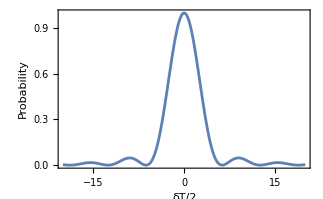

```mathematica
Plot[T^2(Sinc[δ T/2])^2 /. T->1,{δ,-20,20},PlotRange->Full,Frame->True,FrameLabel->{"δT/2","Probability"}]
```

To analyze the matrix element W_ik we consider the form of the electric field as  E(r_0) = ϵ E(r_0) where ϵ is a unit polarization vector

where d is the matrix element of the component of D̂ along the direction of the electric field, depending on the phase of the states |i⟩, |k⟩ it is possible to make the matrix element a real negative number so we can write

where Ω_1 is said to be the Rabi frequency and the transition probability takes the form

This approach has limited applicability because it is only valid for transition probabilities small compared to unity.

#### Rabi oscillations between two levels

Let’s try to use now a non perturbative approach to calculate the transition probability P_(i -> k) in the quasi-resonant case  of angular frequency ω close to |E_k-E_i|/ℏ. Using the two level atom approximation with states |a⟩, |b⟩ with energies E_a, E_b, if we set E_a = 0 and let ω_0 be the Bohr frequency such E_b-E_a = ℏ ω_0

The free Hamiltonian is

using the form of the interaction Hamiltonian with the Rabi frequency,  the complete Hamiltonian is

Used for simplifications:

```mathematica
$Assumptions = {t>0, δ>0 , Subscript[Ω, 1]>0,ω ∈ Reals,ν ∈ Reals};
```

Define an atomic basis:

```mathematica
atomBasis = QuantumBasis[{"a","b"}];
```

Define the atomic Hamiltonian (we take ℏ = 1):

```mathematica
atomicHamiltonian = h (QuantumOperator["X",atomBasis] Subscript[Ω, 1] Cos[ω t +ϕ]+QuantumOperator[DiagonalMatrix[{0,Subscript[ω, 0]}],atomBasis])
```

h Cos[ϕ+t ω] Ω_1ab+h Cos[ϕ+t ω] Ω_1ba+h ω_0bb

Considering a general initial state , the exponential contemplates the free evolution:

```mathematica
ψi =QuantumState[{Subscript[c, a][t],Subscript[c, b][t] ⅇ^(-ⅈ Subscript[ω, 0] t)},atomBasis]
```

c_a(t)a+ⅇ^(-ⅈ t ω_0) c_b(t)b

The Schrodinger equation  :

```mathematica
schrodingerEq = (ⅈ D[ψi,t] - (atomicHamiltonian/h)@ψi)
```

(ⅈ c_a'(t)-Ω_1 ⅇ^(-ⅈ t ω_0) c_b(t) cos(t ω+ϕ))a+(Ω_1 c_a(t) (-cos(t ω+ϕ))+ⅈ (ⅇ^(-ⅈ t ω_0) c_b'(t)-ⅈ ω_0 ⅇ^(-ⅈ t ω_0) c_b(t))-ω_0 ⅇ^(-ⅈ t ω_0) c_b(t))b

We can get the resulting equations for c_a and c_b:

```mathematica
coefs =SolveValues[ Thread[schrodingerEq["AmplitudeList"]==0],{Subscript[c, a]'[t],Subscript[c, b]'[t]}][[1]]//TrigToExp
```

{-1/2 ⅈ Ω_1 c_b(t) ⅇ^(ⅈ t ω-ⅈ t ω_0+ⅈ ϕ)-1/2 ⅈ Ω_1 c_b(t) ⅇ^(-ⅈ t ω-ⅈ t ω_0-ⅈ ϕ),-1/2 ⅈ Ω_1 c_a(t) ⅇ^(ⅈ t ω+ⅈ t ω_0+ⅈ ϕ)-1/2 ⅈ Ω_1 c_a(t) ⅇ^(-ⅈ t ω+ⅈ t ω_0-ⅈ ϕ)}

Utilizing the Rotating Wave Approximation(RWA) we can discard the terms with exp(|ω + ω_0|)because are rapidly oscillating terms and let δ = ω - ω_0 the detuning from resonance

Define rules to use RWA and replace the detuning:

```mathematica
RWAδrules ={ⅇ^(ⅈ ϕ + ⅈ t ω + ⅈ t Subscript[ω, 0])->0,ⅇ^(-ⅈ ϕ - ⅈ t ω - ⅈ t Subscript[ω, 0])->0,(ⅈ t ω-ⅈ t Subscript[ω, 0])-> ⅈ t δ,(ⅈ t Subscript[ω, 0]-ⅈ t ω)-> -ⅈ t δ};
```

Resulting equations:

```mathematica
eqs = Thread[{Subscript[c, a]'[t],Subscript[c, b]'[t]} == coefs /.RWAδrules]
```

{c_a'(t)==-1/2 ⅈ Ω_1 c_b(t) ⅇ^(ⅈ δ t+ⅈ ϕ),c_b'(t)==-1/2 ⅈ Ω_1 c_a(t) ⅇ^(-ⅈ δ t-ⅈ ϕ)}

Lets solve them for the case  (atom initially at the ground state) and introducing the variable Ω called generalized Rabi frequency:

```mathematica
coefSols = FullSimplify[DSolve[Join[eqs,{Subscript[c, a][0]== 1, Subscript[c, b][0] == 0}],{Subscript[c, a][t],Subscript[c, b][t]},t]] /.{√_->Ω,1/√_->1/ Ω}
```

{{c_a(t)→ⅇ^((ⅈ δ t)/2) (cos((t Ω)/2)-(ⅈ δ sin((t Ω)/2))/Ω),c_b(t)→-(ⅈ Ω_1 ⅇ^(-1/2 ⅈ (δ t+2 ϕ)) sin((t Ω)/2))/Ω}}

We can find the probability that the initial state of the atom |a⟩ transitions to |b⟩ as a function of time, and we plot it for different detunings

Wrapping the solution in a QuantumState dependent on parameters:

```mathematica
solvedState = QuantumState[Values @ coefSols[[1]],atomBasis,"Parameters"->{t,δ,Ω,Subscript[Ω, 1]}];
```

Extracting the probability of finding the atom in |b⟩ state:

```mathematica
probFuncs =(solvedState[t,#,√(1+#^2),1]["Probability"]["b"]& /@ Range[0,3] /. ϕ->0);
```

Plotting the results:

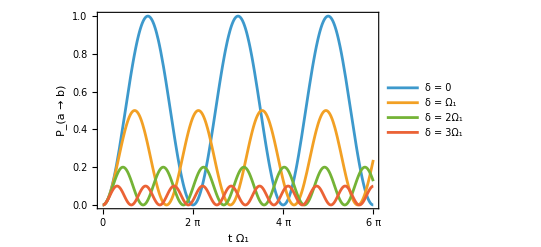

```mathematica
Plot[probFuncs,{t,0,6π},]
```

Is not hard to check from the results that the Rabi oscillations go between 0 and a maximum value , and that value is  . If we consider it as a function of ω it is a Lorentzian profile that has a maximum when the detuning is zero, and the width at half-maximum is 2 Ω_1 dependent of the amplitude of the  electromagnetic field

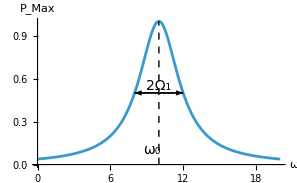

### Atom-field interaction (quantum model two level atom and single mode field)

Having introduced the semiclassical models and field quantization, we can describe the interactions in a fully quantum model. The general multiple-mode field and two-level atom Hamiltonian takes the form:

The Hamiltonian considering only a single-mode field and a two-level atom (after using RWA in the interaction term), results in the Jaynes-Cummings Hamiltonian(JCH):

Annihilation operator (with automatic resizing), the field we will consider in the second qudit:

```mathematica
a := AnnihilationOperator[{2}]
```

Define the atomic basis and the truncation size:

```mathematica
SetFockSpaceSize[50];
atomBasis=QuantumBasis[{"e","g"}];
```

Transition operators  and :

```mathematica
σplus=QuantumOperator["+",atomBasis];
σminus=QuantumOperator["-",atomBasis];
```

Free Hamiltonian:

```mathematica
H0 = QuantumOperator[ 
h ν SuperDagger[a]@a+  1/2 h ω QuantumOperator["Z",atomBasis],
"Parameters"->{ν,ω}];
```

Atom-field interaction term:

```mathematica
H1 = h g (σplus@a +σminus@SuperDagger[a]);
```

Interaction picture Hamiltonian:

```mathematica
HInteract = Simplify[MatrixExp[ⅈ H0/h t]@ H1 @ MatrixExp[-ⅈ H0/h t]];
```

At resonance this Hamiltonian is time independent:

```mathematica
FreeQ[HInteract[ν,ν]["AmplitudeList"],t]
```

True

So we can solve for the evolution operator Û:

```mathematica
U = MatrixExp[-ⅈ HInteract[ν,ν]/h t];
```

#### Solving JCH: Fock state as initial field state

With the time evolution unitary, we can evolve different states let’s start with the simple case of a Fock state:

Build the state |g1⟩:

```mathematica
ψ0 = QuantumState["1",atomBasis]// FockState[1]
```

g1

Evolve the state:

```mathematica
ψt = U @ ψ0
```

-ⅈ sin(g t)e0+cos(g t)g1

Finding the probability of finding the atom in the excited state using a projection:

```mathematica
probE =((SuperDagger[QuantumState["0",atomBasis]]@ψt)["Norm"])^2
```

Abs[sin(g t)]^2

Plotting as function of  T = g t:

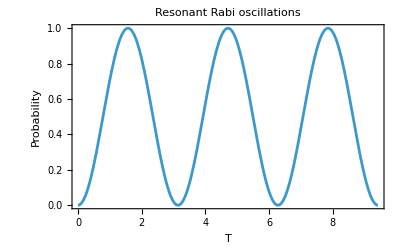

```mathematica
Plot[probE /. g->1 ,{t,0,3π},]
```

We recover the same resonant Rabi oscillations as the semiclassical case, the frequency of the oscillations is dependent on which Fock state is evolved

```mathematica
probs=  Table[{t,n,(SuperDagger[QuantumState["0",atomBasis]]@U@(QuantumState["1",atomBasis]// FockState[n]))["Norm"]},{n,4}];
ParametricPlot3D[Evaluate[probs/.g->1 ,{t,0,3π}],LabelStyle->14,PlotLabel->"Resonant Rabi oscillations",ImageSize->400,PlotLegends->{"|1⟩","|2⟩","|3⟩","|4⟩"},BoxRatios->{3,2,0.5}]
```

-Graphics3D-

#### Solving JC: coherent state as initial field state

Initial state :

```mathematica
ψ0=QuantumState["1",atomBasis]//CoherentState[][5.]["Normalize"];
```

Calculating the evolved state, and the associated c_e(t) and c_g(t) coefficients for each n of the truncated Fock space

Evolved state:

```mathematica
ψt=QuantumState[U@ψ0,"Parameters"->{g,t}];
```

Finding the time dependent  coefficients:

```mathematica
{cet[t_],cgt[t_]} = Values[(SuperDagger[#]@ψt[1,t])["Amplitudes"]& /@ atomBasis["BasisStates"]];
```

For any t, a list is returned of the size of the truncation size(for all n):

```mathematica
Length@cet[0] == $FockSize
```

True

Plotting the population inversion that can be calculated using c_e(t ) and c_g(t). We see collapse and revivals a phenomena only present in the fully quantum model:

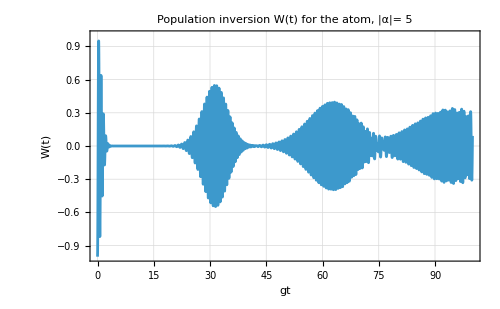

```mathematica
Plot[Evaluate[Total @(Abs[cet[t]]^2-Abs[cgt[t]]^2 )],{t,0,100},]
```

Evolution of the photon number distribution:

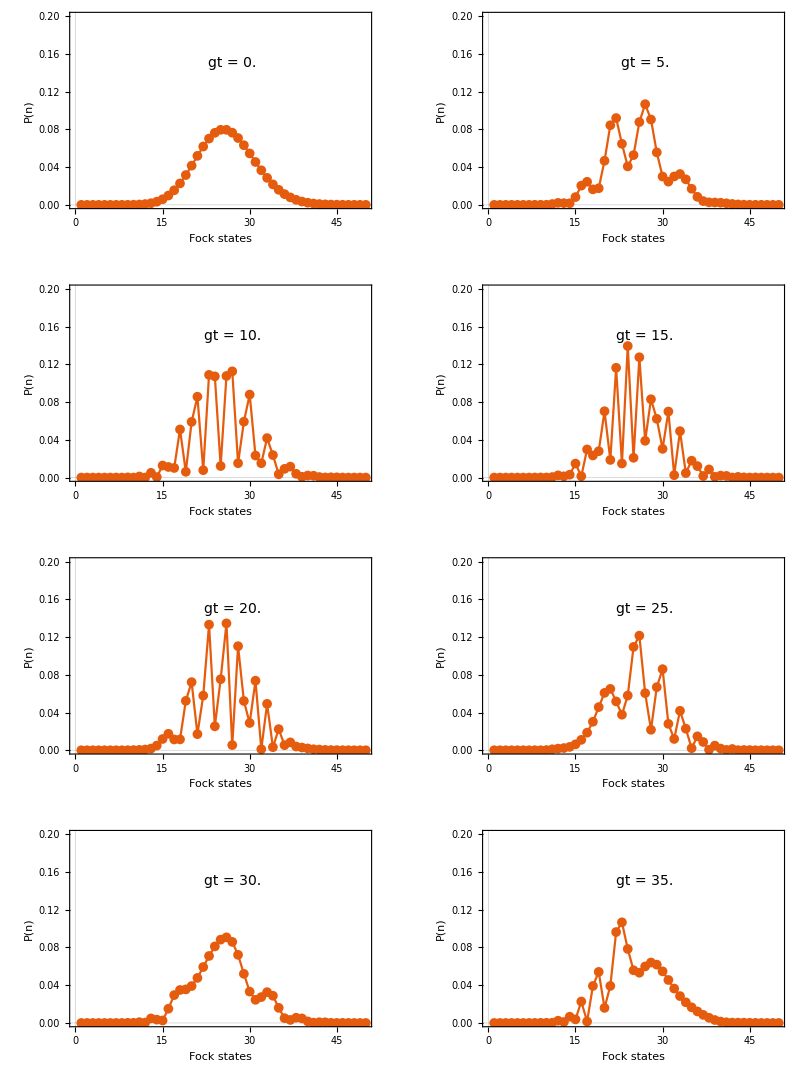

```mathematica
GraphicsGrid@Partition[Table[ListLinePlot[Evaluate[Abs[cet[t]]^2+Abs[cgt[t]]^2],],{t,Range[0,35,5]}],{2}]
```

At g t = 30 the distribution looks similar to the initial one, around that time the revival is more pronounced

#### Density operator applied to thermal states

Atom initially in the superposition   and the field in a thermal state(thermal state will be treated symbolically):

```mathematica
ρ0 = QuantumState["+",atomBasis]//ThermalState[x];
```

ρ_0 is a state of type matrix:

```mathematica
ρ0["StateType"]
```

Matrix

Shortcut for matrix states to describe the evolution ρ(t) =Û(t) ρ(0) (Û)^†(t) :

```mathematica
ρt  = QuantumState[SuperDagger[U][ρ0],"Parameters"->{g,t}];
```

Extracting matrix of the atomic part:

```mathematica
atomMatrix = Normal[QuantumPartialTrace[ρt[1,t],{2}]["DensityMatrix"]]//ComplexExpand;
```

Plotting components, since the thermal state was evolved symbolically the value of x can be changed (of course such that can be represented in the chosen Fock space size):

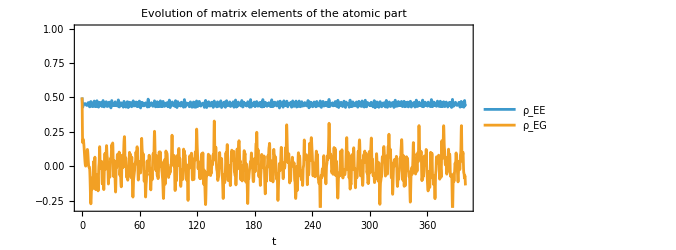

```mathematica
Plot[Evaluate[atomMatrix[[1,{1,2}]]/.x->4.],{t,0,400},]
```

Atom gets “thermalized”, time average of the coherences goes to 0

Time average for one of the coherences:

```mathematica
timeAverages = Integrate[Evaluate[(atomMatrix[[1,2]]/.x->5.)],{t,0,tf}]/tf;
```

Plot the time averages:

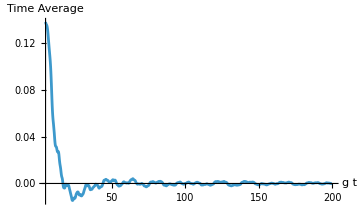

```mathematica
Plot[timeAverages,{tf,5,200},]
```

The atomic inversion is calculated ,   after tracing out the Fock states. Lets calculate the atomic inversion for atom initially excited and field in thermal state with n^— = 5

Redoing the evolution for the state with the atom in the excited state:

```mathematica
ρ0 = QuantumState["0",atomBasis]//ThermalState[5.];
ρt  = QuantumState[SuperDagger[U][ρ0],"Parameters"->{g,t}];
atomMatrix = Normal[QuantumPartialTrace[ρt[1,t],{2}]["DensityMatrix"]];
```

Plot the atomic inversion:

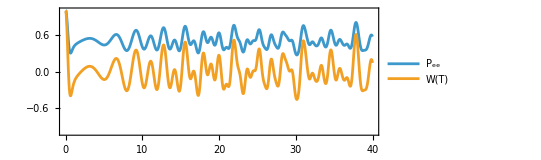

```mathematica
With[{ρe= atomMatrix[[1,1]]},Plot[{ρe,2ρe-1},{t,0,40},]]
```

### Dressed states

Work in a smaller truncation size:

```mathematica
SetFockSpaceSize[12];
```

Returning to the Jaynes Cummings model separating the free and interaction terms:

```mathematica
H0 = QuantumOperator[h ν SuperDagger[a]@a+ 1/2 h ω QuantumOperator["Z",atomBasis],"Parameters"->{ν,ω}];
```

```mathematica
H1 = h g  (σplus@a+σminus@SuperDagger[a]);
```

For a fixed n, the dynamics is determined by the product states |e⟩|n⟩, |g⟩|n+1⟩ (or |e⟩|n-1⟩, |g⟩|n⟩). At near resonance (ν≃ ω), these pairs of states have almost the same energy. For a given n, the bare states are defined:

Bare states implementation:

```mathematica
bareState[i_Integer,n_Integer/; 0<=n<= $FockSize-1]:=atomBasis["BasisStates"][[i+1]]//FockState[n+i]
```

Check for n=10:

```mathematica
{bareState[1,10],bareState[0,10]}
```

{g11,e10}

When we consider the free Hamiltonian the bare states are uncoupled and the energy difference is  related to the detuning   h Δ  (Δ = ν - ω)

Calculating the energy differences of the bare states for the same n:

```mathematica
Differences/@( Table[(H0 @ bareState[m,n])["AmplitudeList"][[1]],{n,0,$FockSize-2},{m,0,1}])
```

{{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω}}

The matrix elements for a given n of bare states, (ℋ^(n))_ij are:

Matrix element calculations

Check ℋ_00:

```mathematica
Table[(bareState[0,n]["Dagger"] @ (H0+H1) @ bareState[0,n])["Scalar"],{n,0,$FockSize-2}]==Array[Expand[h(# ν + 1/2 ω)]&,$FockSize-1,0]
```

True

Check ℋ_11:

```mathematica
Table[(bareState[1,n]["Dagger"] @ (H0+H1) @ bareState[1,n])["Scalar"],{n,0,$FockSize-2}]== Array[Expand[h((#+1) ν - 1/2 ω)]&,$FockSize-1,0]
```

True

Check ℋ_01:

```mathematica
Table[(bareState[0,n]["Dagger"] @ (H0+H1) @ bareState[1,n])["Scalar"],{n,0,$FockSize-2}]== Array[Expand[h(g √(#+1))]&,$FockSize-1,0]
```

True

With those matrix elements we can generate a matrix that contains the dynamics (because of the interaction term of the Hamiltonian) of a 2x2 subspace for a given n:

Dressed subspace operator:

```mathematica
dressedSubspace = QuantumOperator[{{h(n ν +1/2  ω),h g √(n+1)},{h g √(n+1), h((n+1) ν -1/2 ω)}}]
```

h (n ν+ω/2)00+g h √(1+n)01+g h √(1+n)10+h ((1+n) ν-ω/2)11

Calculate the eigenvalues (express in terms of the detuning):

```mathematica
eigenvals =ReplaceAll[#,{(ν-ω)->Δ}]& /@(dressedSubspace["Eigenvalues"])
```

{1/2 h (-√(Δ^2+4 g^2 (n+1))+ν+2 ν n),1/2 h (√(Δ^2+4 g^2 (n+1))+ν+2 ν n)}

With the interaction Hamiltonian there is an energy shift  hΩ_n(Δ) (when g = 0 there is no interaction and we recover the previous result) Ω_n(Δ) = √(4g^2(n+1) + Δ^2) (generalized Rabi frequency). The energy splitting of the states is also called AC Stark Shift

Calculate energy shift:

```mathematica
eigenvals//Differences //Simplify
```

{h √(Δ^2+4 g^2 (n+1))}

The eigenstates associated with the energy eigenvalues have the following form:

such that

and   ,

Calculate the eigenvectors, and re-express the variables:

```mathematica
eigenVecs = FullSimplify[(dressedSubspace["Eigenvectors"]//. {ν-ω->Δ,-ν+ω->-Δ,√(4 g^2 (1+n)+Δ^2)->Subscript[Ω, n]}) ,Element[{Subscript[Ω, n],g,n,Δ},Reals] && Subscript[Ω, n]>Δ>0 && n>=0 && g>0 ];
```

"Eigenvectors"  finds a different set of valid eigenvectors of the form {-cos(Φ), sin(Φ)} and {sin(Φ), cos(Φ)}:

```mathematica
simplifiedDressedEigenvecs = FullSimplify[#/.{ 1/(g^2(n+1))->4/( Subscript[Ω, n]^2-Δ^2), 4 g^2(n+1)->Subscript[Ω, n]^2-Δ^2 },Subscript[Ω, n]>0 && Δ>0]& /@ eigenVecs //Together
```

{{-(√((Δ+Ω_n)/Ω_n))/(√2),1/(√2 √(Ω_n/(-Δ+Ω_n)))},{(√((-Δ+Ω_n)/Ω_n))/(√2),(√((Δ+Ω_n)/Ω_n))/(√2)}}

When Δ = 0 the bare states are degenerate   but the splitting remains   :

```mathematica
dressedSubspace["Eigenvalues"]/. ν->ω //Differences//Simplify
```

{2 h √(g^2 (n+1))}

In this limit the dressed states are related to the bare states as

Test that limit(we negate first components to follow the literature convention):

```mathematica
MapAt[-#&,simplifiedDressedEigenvecs /. Δ->0,{{1,1},{2,1}}]
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

The dressed states are stationary states of the atom-field system, so the evolution can be described in this basis as

### Schmidt decomposition and von Neumann entropy for Jaynes-Cummings

A bipartite system always has a Schmidt decomposition; the general time-dependent state in bare basis is:

Using Schmidt decomposition, it is possible to find for any time , bases {|u_i(t)⟩} for the atom and {|v_i(t)⟩} for the field such that:

In those bases, the reduced density matrices of the atom and field are the same:

Analytical form of the reduced atomic density matrix

Employing the parametrization of the density matrix in terms of Bloch vector components, it is possible to obtain the relations

Arbitrary state specified as a 2x2 density matrix :

```mathematica
state = QuantumState[{{Subscript[b, 11],Subscript[b, 12]},{Subscript[b, 21],Subscript[b, 22]}}];
```

```mathematica
state["DensityMatrix"]//MatrixForm
```

(b_11 | b_12
b_21 | b_22)

Bloch vector expressed in terms of the components of the matrix:

```mathematica
state["BlochVector"]
```

{b_12+b_21,ⅈ b_12-ⅈ b_21,b_11-b_22}

And the g coefficients are calculated as a function of the length of the Bloch vector

Von Neumann entropy for each of the subsystems:

Return to the previous Fock space size:

```mathematica
SetFockSpaceSize[50];
```

Initial state (atom excited and field coherent state with |α|=5):

```mathematica
ψ0 = QuantumState["0",atomBasis]//CoherentState[][5.]["Normalize"];
```

Evolved state:

```mathematica
ψt = QuantumState[(U@ψ0),"Parameters"->{g,t}];
```

Bloch vector of reduced density matrix:

```mathematica
blochVector =QuantumPartialTrace[U@ψ0,{2}]["BlochVector"] /. g t->T;
```

Plot of the s_i components (s_1 is zero for this given initial state  and s_3 corresponds to the atomic population inversion) :

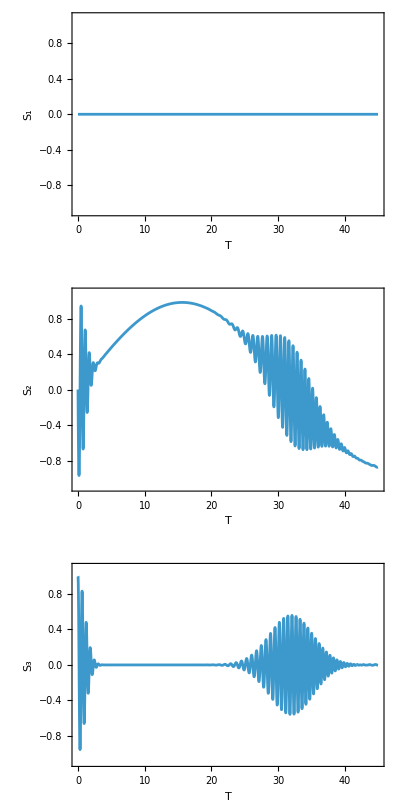

```mathematica
Labeled[GraphicsColumn[Table[Plot[blochVector⟦i⟧,{T,0,45},],{i,3}]],,Top]
```

Norm of the Bloch vector:

```mathematica
normBloch = Norm[blochVector];
```

Extracting the g coefficients:

```mathematica
{g1,g2}= {1/2(1+normBloch),1/2(1-normBloch)};
```

Calculating the Von Neumann entropy:

```mathematica
vonneumann= -g1 Log[g1]-g2 Log[g2];
```

Plot entropy as function of time:

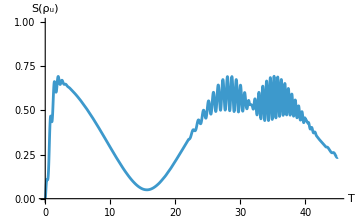

```mathematica
Plot[vonneumann ,{T,0,45},PlotRange->{0,1},AxesLabel->{"T","S(ρ_u)"},LabelStyle->12]
```

Wolfram QuantumFramework supports “SchmidtBasis” and “SchmidtDecompose” properties for quantum states

Verifying g1 and g2 coincide with the amplitudes of “SchmidtBasis” for some particular time:

```mathematica
√({g1,g2} /. T->2.4)
```

{0.798282,0.602284}

```mathematica
ψt[1,2.4]["SchmidtBasis"]
```

0.798282u_1 v_1+0.602284u_2 v_2

Get the reduced density matrices in this basis:

```mathematica
Table[QuantumPartialTrace[ψt[1,2.4]["SchmidtBasis"],{i}],{i,2}];
```

Check that in this basis both have equivalent forms:

```mathematica
%//TraditionalForm
```

{0.637254v_1v_1+0.362746v_2v_2,0.637254u_1u_1+0.362746u_2u_2}

We can also directly compute "VonNeumannEntropy" for a QuantumState, getting the same result as before:

Atomic part of the evolved state:

```mathematica
evol = QuantumState[QuantumPartialTrace[U@ψ0,{2}],"Parameters"->{g,t}];
```

Plot “VonNeumannEntropy”:

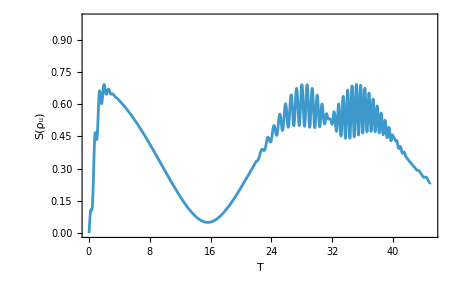

```mathematica
Plot[evol[1,t]["VonNeumannEntropy"]Log[2],{t,0,45},PlotRange->{0,1},Frame->True,FrameLabel->{"T","S(ρ_u)"},LabelStyle->14]
```

Function to minimize:

```mathematica
func[t_?NumericQ]:=QuantityMagnitude[evol[1,t]["VonNeumannEntropy"]Log[2]]
```

Finding the time of the local minimum of entropy:

```mathematica
Tmin =FindMinimum[func[t],{t,5}][[2]]
```

{t→15.654}

The maximum of s_2 corresponds to a minimum of the Von Neumann entropy, which can be understood as the time where the reduced density matrices of the atom-field system are approximately pure (happens at around T = gt ≈ 15.6 for this example)

Use the “Purity” property at the calculated time:

```mathematica
Table[QuantumPartialTrace[ψt[1,t/.Tmin],{i}]["Purity"],{i,2}]
```

{0.982672,0.982672}

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Exercises

Define using the Quantum Framework a modified Jaynes-Cummings Hamiltonian, such that the atom has three levels, two ground states and one excited state. Find the state ψ(t) as a function of time for the initial state 1/(√3)(|e⟩ + |g_1⟩ + |g_2⟩ ) ⊗ |1⟩

Solution

Define the field truncation size and the annihilation operator:

SetFockSpaceSize[30];
a := AnnihilationOperator[{2}]

Define the new basis:

atomBasis = QuantumBasis[{"e","g_1","g_2"}];

Modified atomic transition operators:

σplus =QuantumOperator[PadRight[{{0,1,1}},{3,3}],atomBasis];
σminus = σplus^†;

Column[{σplus,σminus}]//TraditionalForm

"e""g_1"+"e""g_2"
"g_1""e"+"g_2""e"

Free Hamiltonian:

H0 = QuantumOperator[ 
h ν a^†@a+  1/2 h ω QuantumOperator[DiagonalMatrix[{1,-1,-1}],atomBasis],
"Parameters"->{ν,ω}];

Interaction part:

H1 = h g (σplus@a +σminus@a^†);

Going to the interaction picture:

HInteract = Simplify[MatrixExp[ⅈ H0/h t]@ H1 @ MatrixExp[-ⅈ H0/h t]];

Finding the unitary operator:

U = MatrixExp[-ⅈ HInteract[ν,ν]/h t];

Evolve the requested state:

Simplify@U[QuantumState[1/(√3){1,1,1},atomBasis]//FockState[1]]

-ⅈ √(2/3) sin(√2 g t)"e"0+(cos(2 g t))/(√3)"e"1+(cos(√2 g t))/(√3)"g_1"1-(ⅈ sin(2 g t))/(√6)"g_1"2+(cos(√2 g t))/(√3)"g_2"1-(ⅈ sin(2 g t))/(√6)"g_2"2

Following on the previous exercise, using this model find the dark states of the atom-field system. This amounts to finding states ψ such that H_I |ψ⟩ = 0

Solution

Find the eigensystem of the interaction Hamiltonian:

{vals,vecs}=N[HInteract]["Eigensystem"];

Show the possible dark states:

TraditionalForm[QuantumState[#,{atomBasis,$FockSize}]&/@Extract[vecs,Position[vals,0]]]

{-0.707107"g_1"29+0.707107"g_2"29,-0.707107"g_1"28+0.707107"g_2"28,-0.707107"g_1"27+0.707107"g_2"27,-0.707107"g_1"26+0.707107"g_2"26,-0.707107"g_1"25+0.707107"g_2"25,-0.707107"g_1"24+0.707107"g_2"24,-0.707107"g_1"23+0.707107"g_2"23,-0.707107"g_1"22+0.707107"g_2"22,-0.707107"g_1"21+0.707107"g_2"21,-0.707107"g_1"20+0.707107"g_2"20,-0.707107"g_1"19+0.707107"g_2"19,-0.707107"g_1"18+0.707107"g_2"18,-0.707107"g_1"17+0.707107"g_2"17,-0.707107"g_1"16+0.707107"g_2"16,-0.707107"g_1"15+0.707107"g_2"15,-0.707107"g_1"14+0.707107"g_2"14,-0.707107"g_1"13+0.707107"g_2"13,-0.707107"g_1"12+0.707107"g_2"12,-0.707107"g_1"11+0.707107"g_2"11,-0.707107"g_1"10+0.707107"g_2"10,-0.707107"g_1"9+0.707107"g_2"9,-0.707107"g_1"8+0.707107"g_2"8,-0.707107"g_1"7+0.707107"g_2"7,-0.707107"g_1"6+0.707107"g_2"6,-0.707107"g_1"5+0.707107"g_2"5,-0.707107"g_1"4+0.707107"g_2"4,-0.707107"g_1"3+0.707107"g_2"3,-0.707107"g_1"2+0.707107"g_2"2,-0.707107"g_1"1+0.707107"g_2"1,1."g_2"0,1."g_1"0,1."e"29}

So the requested state has the form 1/(√2)(|g_1⟩ - |g_2⟩) ⊗ |n⟩, for n ≥ 1:

With[{n= RandomInteger[{1,$FockSize-1}]},HInteract[QuantumState[1/(√2){0,1,-1}]//FockState[n]]]

0

Consider the atom-field Hamiltonian  without using the rotating wave approximation, this means keeping also terms that are not energy preserving (σ_x is used). Use values of strong coupling ω_c/g ≈ 0.5  , initial state |e,0⟩  and plot the concurrence and the Rabi oscillations as function of time. Also visualize the Wigner function of the field system at times when there is high atom-field entanglement.

Solution

Define the atomic basis:

atomBasis = QuantumBasis[{"e","g"}];

σplus = QuantumOperator["+",atomBasis];
σminus = QuantumOperator["-",atomBasis];

Define the Hamiltonian:

H =QuantumOperator[ωc a^†@a+ ωr/2 QuantumOperator["Z",atomBasis]+ g QuantumTensorProduct[QuantumOperator["X",atomBasis],a+a^†],"Parameters"->{ωc,ωr,g}];

Initial state:

ψ0 = QuantumState["0",atomBasis]//FockState[0];

Numerical evolution:

evolved =QuantumEvolve[H[1.,0.9,0.5],ψ0,{t,0,50}];

Concurrence plot:

Plot[QuantumEntanglementMonotone[evolved[t],{{1},{2}}],{t,0,50}]

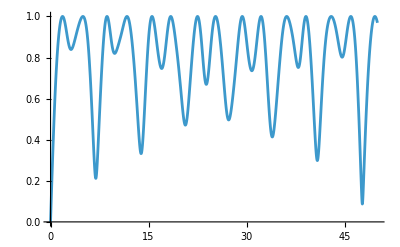

“Rabi” oscillations:

Plot[QuantumPartialTrace[evolved[t],{2}]["DensityMatrix"][[1,1]],{t,0,50}]

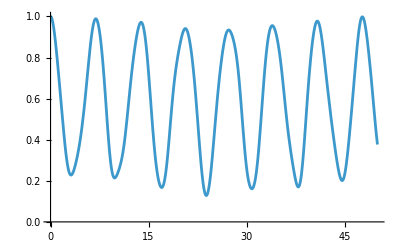

Phase space plots:

plots =Table[wig = WignerRepresentation[QuantumPartialTrace[evolved[t],{1}],{-4,4},{-4,4}];
DensityPlot[wig[x,p],{x,-4,4},{p,-4,4},PlotPoints->80,PlotRange->All,ColorFunction->"SolarColors",FrameLabel->{"x","p"},PlotLegends->Placed[Automatic, Top]],{t,{1.7,5.2,8.8,11.5}}];

Grid@Partition[plots,2]

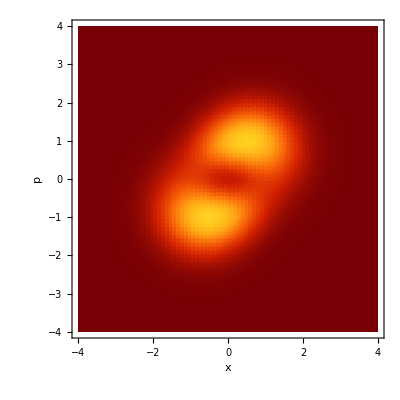
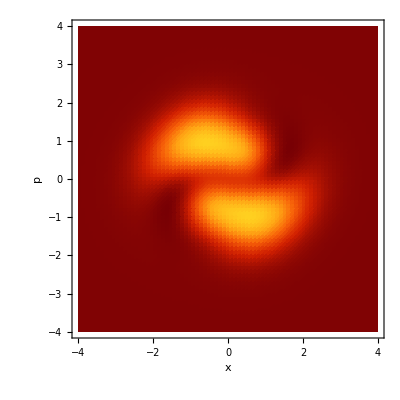
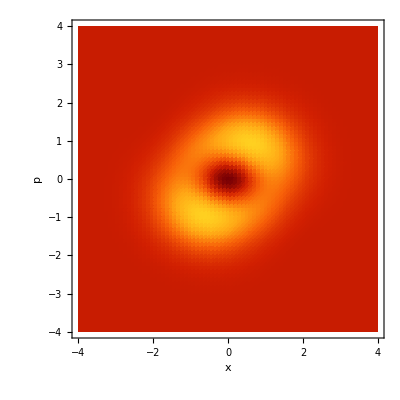
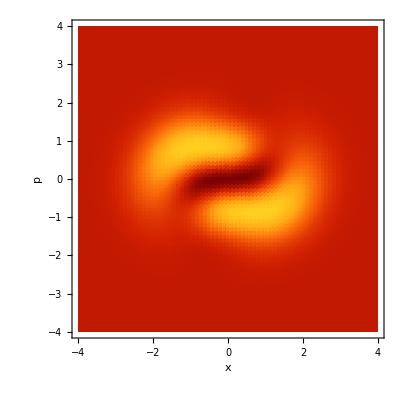
-Graphics- | -Graphics-
-Graphics- | -Graphics-